```mathematica
f[x_]=√3*Exp[-1/22*x^3 +1/2*x-1/4]
```

√3 ⅇ^(-1/4+x/2-x^3/22)

```mathematica
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
```

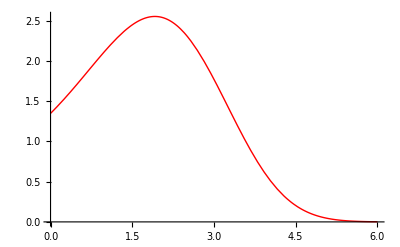

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
(*Возьмём таблицу значений функции для равноотстоящих узлов(Subscript[h, i] =h) на промежутке для n=10:*)
```

```mathematica
data=Table[{i h,f[i h]},{i,0,n}]//N;
TableForm[data]
```

0. | 1.34892
0.6 | 1.80306
1.2 | 2.27223
1.8 | 2.54522
2.4 | 2.38916
3. | 1.77187
3.6 | 0.978807
4.2 | 0.379717
4.8 | 0.0975292
5.4 | 0.0156365
6. | 0.00147533

```mathematica
(*Для получения кубического сплайна дефекта 1 найдём коэффициенты Subscript[c, k] с помощью встроенной функцииLinearSolve.*)
listC=Table[0,{i,0,n}];
A=Table[0,{n-1},{n-1}];
Do[If[i≠1,A[[i,i-1]]=h];A[[i,i]]=4 h;If[i≠n-1,A[[i,i+1]]=h],{i,1,n-1}]
```

```mathematica
A//MatrixForm//N
```

(2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4)

```mathematica
(*Столбец свободных членов:*)
```

```mathematica
B=Table[3 ((data[[i,2]]-data[[i-1,2]])/h-(data[[i-1,2]]-data[[i-2,2]])/h),{i,3,n+1}]//N;
```

```mathematica
X=LinearSolve[A,B];
```

```mathematica
For[i=1,i≤n-1,i++,listC[[i+1]]=X[[i]]];
```

```mathematica
MatrixForm[listC]
```

(0
0.0995431
-0.273003
-0.642322
-0.733053
-0.269145
0.34493
0.505836
0.272581
0.0729624
0)

```mathematica
(*Зададим остальные коэффициенты кубического сплайна:*)
listA=Table[data[[i+1,2]],{i,1,n}]
```

{1.80306,2.27223,2.54522,2.38916,1.77187,0.978807,0.379717,0.0975292,0.0156365,0.00147533}

```mathematica
listB=Table[(data[[i,2]]-data[[i-1,2]])/h+2/3 h listC[[i]]+1/3 h listC[[i-1]],{i,2,n+1}]
```

{0.796721,0.692645,0.14345,-0.681775,-1.28309,-1.23762,-0.727163,-0.260113,-0.0527869,-0.00900945}

```mathematica
listD=Table[(listC[[i]]-listC[[i-1]])/(3 h),{i,2,n+1}]
```

{0.0553017,-0.20697,-0.205177,-0.0504062,0.257727,0.341153,0.0893923,-0.129587,-0.110899,-0.0405347}

```mathematica
(*Теперь зададим кубический сплайн в виде кусочно заданной функции:*)
sData=Table[{listA[[i]]+listB[[i]] (x-data[[i+1,1]])+listC[[i+1]] (x-data[[i+1,1]])^2+listD[[i]] (x-data[[i+1,1]])^3,data[[i,1]]≤x≤data[[i+1,1]]}, {i,1,n}]//Simplify
```

```mathematica
S[x_]=Piecewise[sData]
```

Piecewise[{{1.34892+0.736995 x+1.38778×10^-17 x^2+0.0553017 x^3, 0.≤x≤0.6}, {1.40557+0.453742 x+0.472089 x^2-0.20697 x^3, 0.6≤x≤1.2}, {1.40247+0.461488 x+0.465634 x^2-0.205177 x^3, 1.2≤x≤1.8}, {0.499851+1.96586 x-0.370128 x^2-0.0504062 x^3, 1.8≤x≤2.4}, {-3.75978+7.2904 x-2.58869 x^2+0.257727 x^3, 2.4≤x≤3.}, {-6.01229+9.54291 x-3.33952 x^2+0.341153 x^3, 3.≤x≤3.6}, {5.73386-0.24555 x-0.620506 x^2+0.0893923 x^3, 3.6≤x≤4.2}, {21.9576-11.8339 x+2.13863 x^2-0.129587 x^3, 4.2≤x≤4.8}, {19.8909-10.5422 x+1.86953 x^2-0.110899 x^3, 4.8≤x≤5.4}, {8.81102-4.38675 x+0.729624 x^2-0.0405347 x^3, 5.4≤x≤6.}, {0, True}}]

```mathematica
(*Изобразим полученный кубический сплайн.*)
graphD=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graphS=Plot[S[x],{x,a,b}];
```

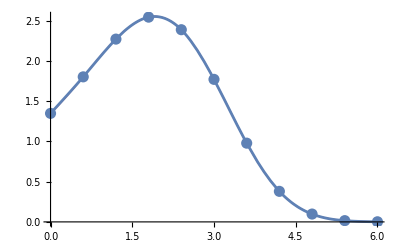

```mathematica
Show[graph,graphD,graphS]
```

```mathematica
(*б*)

(*Интерполируем функцию сплайном с помощью функцииInterpolation:*)
Sf[x_]=Interpolation[data,x,Method->"Spline"]
```

InterpolatingFunction[…][x]

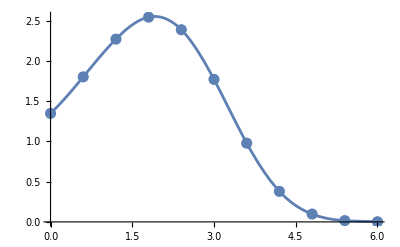

```mathematica
graphSf=Plot[Sf[x],{x,a,b}];
Show[graph,graphD,graphSf]
```

```mathematica
(*в*)

(*Получим интерполяционный кубический сплайн с помощью функцииSplineFit:*)
Needs["Splines`"]
```

```mathematica
Spl=SplineFit[data,Cubic]
```

SplineFunction[Cubic, {0.,10.}, <>]

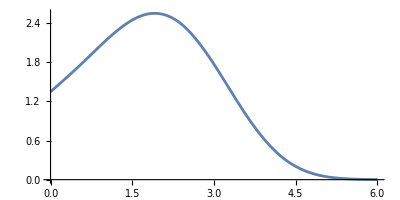

```mathematica
t=(x-a)/h;
graphSpl=ParametricPlot[Spl[t],{t,0,n},AspectRatio->1/2]
```

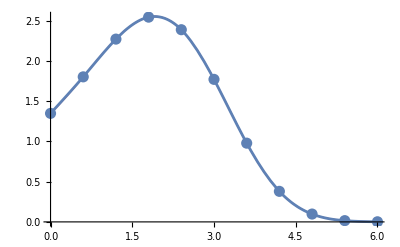

```mathematica
Show[graph,graphD,graphSpl]
```

```mathematica
(*г*)
(*Значение интерполяционного кубического сплайна в точке x0:*)
Print["S[x0]=",S[x0]]
```

S[x0]=2.36689

```mathematica
(*Значение интерполирующей функции-сплайна в точке x0:*)
Print["Sf[x0]=",Sf[x0]]
```

Sf[x0]=2.36688

```mathematica
(*Значение интерполяционного кубического сплайна,построенного с помощьюSplineFit,в точке x0:*)
```

```mathematica
Print["Spl[x0]=",Last[Spl[(x0-a)/h]]]
```

Spl[x0]=2.36689